```mathematica
;
```

Last updated:   Thu 13 Jan 2022

## About Jazz

```mathematica
(* set text style *)
SetOptions[Style,FontSize->15,FontFamily->"Avenir Next"];
styleOpts=Sequence[FontSize->15,FontFamily->"Avenir Next"];
```

```mathematica
extractInfo[items_List]:=
```

```mathematica
(* summary of Wikipedia article *)
```

Jazz is a music genre that originated in the African-American communities of New Orleans, Louisiana, United States, in the late 19th and early 20th centuries, with its roots in blues and ragtime. Since the 1920s Jazz Age, it has been recognized as a major form of musical expression in traditional and popular music, linked by the common bonds of African-American and European-American musical parentage. Jazz is characterized by swing and blue notes, complex chords, call and response vocals, polyrhythms and improvisation. Jazz has roots in West African cultural and musical expression, and in African-American music traditions.As jazz spread around the world, it drew on national, regional, and local musical cultures, which gave rise to different styles. New Orleans jazz began in the early 1910s, combining earlier brass-band marches, French quadrilles, biguine, ragtime and blues with collective polyphonic improvisation. In the 1930s, heavily arranged dance-oriented swing big bands, Kansas City jazz, a hard-swinging, bluesy, improvisational style and gypsy jazz (a style that emphasized musette waltzes) were the prominent styles. Bebop emerged in the 1940s, shifting jazz from danceable popular music toward a more challenging "musician's music" which was played at faster tempos and used more chord-based improvisation. Cool jazz developed near the end of the 1940s, introducing calmer, smoother sounds and long, linear melodic lines.
The mid-1950s saw the emergence of hard bop, which introduced influences from rhythm and blues, gospel, and blues, especially in the saxophone and piano playing. Modal jazz developed in the late 1950s, using the mode, or musical scale, as the basis of musical structure and improvisation, as did free jazz, which explored playing without regular meter, beat and formal structures. Jazz-rock fusion appeared in the late 1960s and early 1970s, combining jazz improvisation with rock music's rhythms, electric instruments, and highly amplified stage sound. In the early 1980s, a commercial form of jazz fusion called smooth jazz became successful, garnering significant radio airplay. Other styles and genres abound in the 2000s, such as Latin and Afro-Cuban jazz.

```mathematica
(* some properties of Wikidata entry *)
WikidataData[ExternalIdentifier["WikidataID","Q8341",<|"Label"->"jazz","Description"->"musical genre and theory"|>]"Wikidata""jazz"http://www.wikidata.org/entity/Q8341,"NonIdentifierProperties","Dataset"][;;,extractInfo]
```

Dataset[<>]

```mathematica
(* get Wiki article*)
jazzArticleText=;
```

```mathematica
(* clean text (lower case -> delete stopwords -> remove diacritics) -> plot word cloud *)
:=;
```

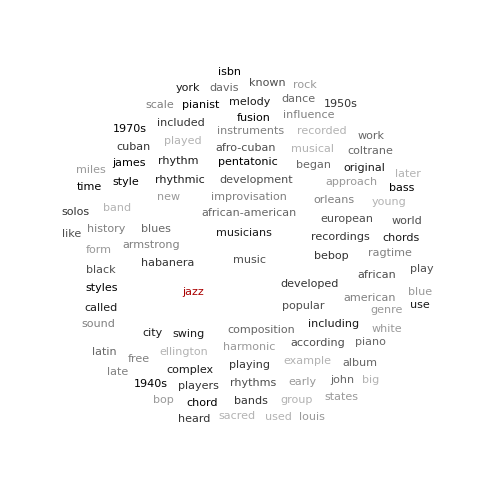
-Graphics- |  —  — jazz390
 —  — music129
 —  — new82
 —  — musicians72
 —  — blues49
 —  — band42
 —  — bebop37
 —  — style36
 —  — orleans36
 —  — swing32
 —  — early32
 —  — african32
 —  — musical29
 —  — began29
 —  — popular28
 —  — fusion28
 —  — free28
 —  — bands28
 —  — rhythm27
 —  — form27

```mathematica
createWordCloud[jazzArticleText,20,"jazz"]
```

### In language and books

```mathematica
(* plot options *) plotOpts=;
(* search period *) wfPeriod={1900,Now@"Year"};
```

```mathematica
(* frequencies in published English texts, incl. spelling case variants (showing only top 3) *)
ReverseSort[Dataset@ReverseSort@WordFrequencyData["jazz","CaseVariants",wfPeriod]][[;;3]];
(* total *)
Panel@Labeled[Highlighted[Total[%]],"Total frequency",Top];
Row[{%%,%},Spacer[5]]
```

7.28241×10^-6Total frequency

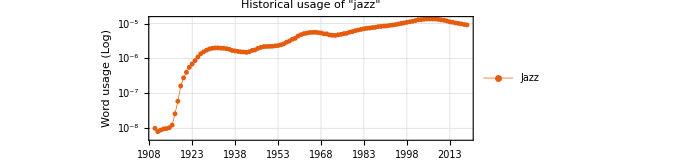

```mathematica
(* 10-yr moving average of word usage (case ignored) *)
```

```mathematica
(* connect to OpenLibrary API *)
openlibrary=ServiceConnect["OpenLibrary"];
(* func for getting book data *)
getBookData[title_]:=getBookData[title]=
```

```mathematica
(* titles *)
bookTitles=;
Panel@Labeled[Highlighted@Length@bookTitles,"No. of books from OpenLibrary API",Top]
(* publication dates *)
pubDates=;
MinMax@pubDates
```

7093No. of books from OpenLibrary API

{Year: 1899,Year: 2022}

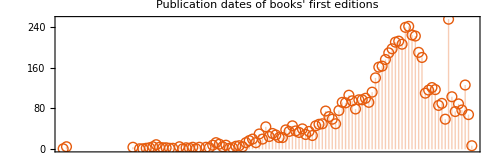

```mathematica
(* books' first publish dates (1st editions) *)
```

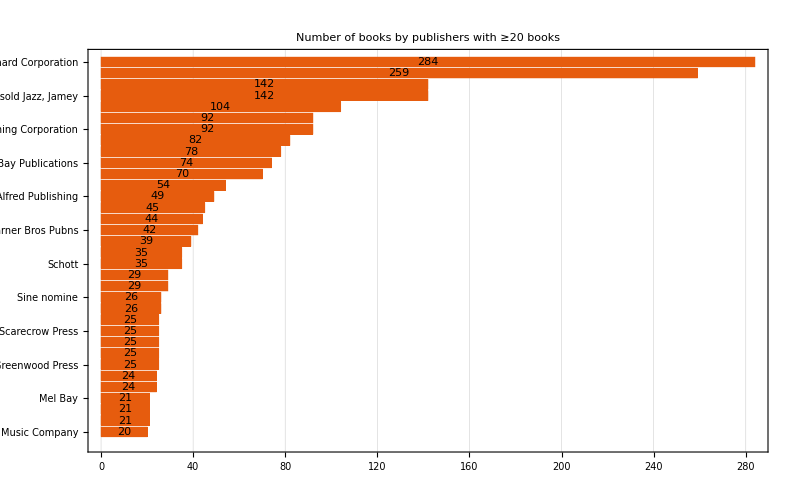

```mathematica
(* no. of books by each publisher (≥20 only) *)
```

```mathematica
(* plot freq of pub's & word use *)
```

-Graphics-Historical frequencies of book publications and word usage

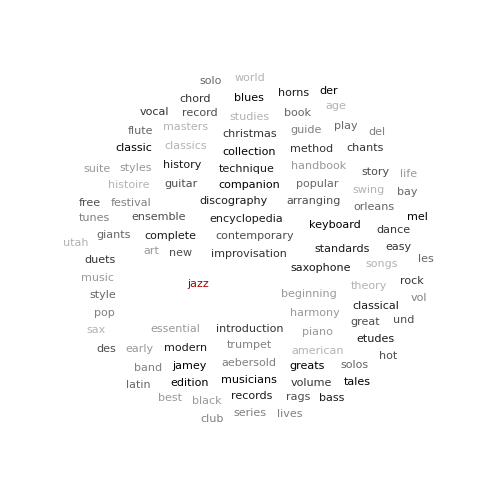
-Graphics- |  —  — jazz5124
 —  — guitar230
 —  — piano227
 —  — standards117
 —  — book112
 —  — age97
 —  — improvisation92
 —  — guide91
 —  — blues82
 —  — new80
 —  — music73
 —  — history71
 —  — solos69
 —  — classics65
 —  — dance57
 —  — del56
 —  — mel51
 —  — styles48
 —  — great48
 —  — complete45

```mathematica
(* wordcloud of book titles *)
```

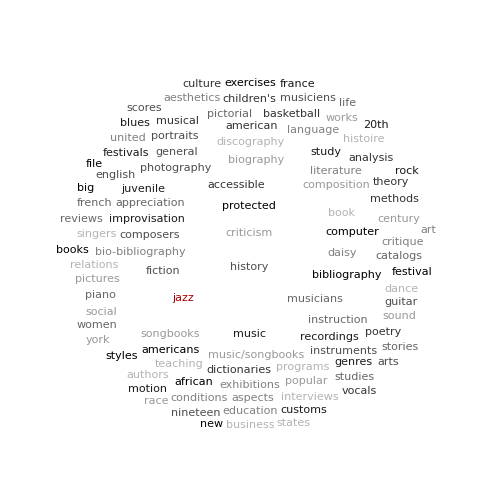
-Graphics- |  —  — jazz3317
 —  — history1289
 —  — criticism1150
 —  — music1109
 —  — musicians824
 —  — book746
 —  — accessible745
 —  — protected689
 —  — daisy689
 —  — fiction329
 —  — biography321
 —  — study265
 —  — instruction242
 —  — discography229
 —  — american187
 —  — literature183
 —  — african173
 —  — general158
 —  — social149
 —  — juvenile138

```mathematica
(* wordcloud of book subjects *)
```

```mathematica
(* counts by author name *)
bookAuthorCounts=;
Select[bookAuthorCounts,#>10&]
```

<|Mark C. Gridley→26,Alfred Publishing→24,F. Scott Fitzgerald→26,Paul Tanner→11,Hal Leonard Corp.→135,Nat Hentoff→12,Richard Cook→13,Leonard Feather→27,Jerry Coker→11,Carolyn Graham→17,Ted Gioia→14,Dan Haerle→14,John Fordham→13,Jody Fisher→17,Martin T. Williams→13,Martin Williams→11,Hugues Panassié→11,Brent Edstrom→11,Various→19,Hal Leonard Corp. Staff→28,David N. Baker→19,Martha Mier→11,Frank Mantooth→11,Bill Boyd→14,Jamey Aebersold→26,David Baker→12,Bob Phillips→11,Randy Sabien→11|>

```mathematica
(* no.s of books by/accredited to musicians *)
booksByMusicians=
```

<|Wynton Marsalis→5,Oscar Peterson→6,Buddy Rich→2,Joe Pass→2,Mike Zwerin→2,London Philharmonic Orchestra→2,Johann Sebastian Bach→1,Paul Whiteman→2,David Houston→2,Andrew Lloyd Webber→2,Igor Stravinsky→1,Buck Clayton→4,Teddy Wilson→1,Artie Shaw→1,Little Milton→1,J.J. Johnson→1,Wayne Shorter→1,Bill Evans→1,Janelle Monáe→1,Clutch→1,Johannes Brahms→1,Jelly Roll Morton→1,The Dave Brubeck Quartet→1,Charlie Parker→1,Clint Eastwood→1,George Gershwin→1,Miles Davis→2,Dave Brubeck→4,Oscar Pettiford→1,Wes Montgomery→2,John Michael Montgomery→1,Neil Diamond→1,Thelonious Monk→1,Bryan White→1,Bix Beiderbecke→1,Duke Ellington→4,James P. Johnson→1,Chet Baker→1,Benny Goodman→3,Throbbing Gristle→1,Giuseppe Verdi→1,Bud Freeman→1,Henry Mancini→1,Mike WiLL Made-It→2,Elton John→2,George Benson→1,Jamie Cullum→1,Bobby Brown→1,Barney Kessel→2,Tal Farlow→2,Cole Porter→1,Dizzy Gillespie→1,Ornette Coleman→1,Ray Brown→1,The Beatles→2,Woody Shaw→1,John Coltrane→1,Stevie Wonder→1,Billy Joel→2,Pat Metheny→1,Quincy Jones→1,Sonny Rollins→1|>

## Jazz musicians

The Wikipedia page "List of jazz musicians" contains a list of musicians for which there a Wikipedia article exist. Conveniently, the musicians are grouped by instruments. Some instrument categories are listed here, while others linked to a separate Wikipedia page of list for that particular instrument.

To get the other lists, we can get all links in the current article (“List of jazz musicians”) and parse it and extract links that are likely to be instrument-specific (e.g., containing ‘List of,’ and ending with ‘ists’ [instrument] or ‘musicians’ [genre]). It’s worth taking a look at the category page "Category:Lists of jazz musicians" too. There are many sub-genres of Jazz and certainly many more different types of instruments involved. I will only focus on some and not all of these.

```mathematica
(* get articles with lists *)
listArticleTitles=
```

{List of bebop musicians,List of chamber jazz musicians,List of cool jazz and West Coast jazz musicians,List of hard bop musicians,List of jazz banjoists,List of jazz bassists,List of jazz fusion musicians,List of jazz guitarists,List of jazz organists,List of jazz percussionists,List of jazz pianists,List of jazz saxophonists,List of jazz trombonists,List of jazz vibraphonists,List of jazz violinists,List of jazz vocalists,List of smooth jazz musicians,List of soul jazz musicians,List of swing musicians}

Those are the links to other lists. As for the musicians listed on this list, we need to do some parsing to extract them:

```mathematica
(* get article -> parse to paragraphs -> drop headings w/ links -> split strings @ new lines *)
parsedLists=;
(* display lists grouped by instrument *)

(* alternative display *)
;
```

Instrument | Examples | No. of Musicians
Accordion |  |  | Kamil Běhounek (1916–1983)Luciano Biondini (born 1971)Asmund Bjørken (1933–2018)Stian Carstensen (born 1971) | 19
Bass guitar |  |  | Victor Bailey (1960–2016)Brian Bromberg (born 1960)Stanley Clarke (born 1951)Bob Cranshaw (1932–2016) | 15
Bassoon |  |  | Garvin Bushell (1902–1991)Karen Borca (born 1948)Yusef Lateef (1920–2013)Illinois Jacquet (1922–2014) | 7
Cello |  |  | Harry Babasin (1921–1988)Ron Carter (born 1937)David Darling (born 1941)Richard Davis (born 1930) | 16
Clarinet |  |  | Woody Allen (born 1935)Craig BallBarney Bigard (1906–1980)Don Burrows (1928–2020) | 31
Cornet |  |  | Nat Adderley (1931–2000)Louis Armstrong (1901–1971)Bix Beiderbecke (1903–1931)Buddy Bolden (1877–1931) | 12
Flugelhorn |  |  | Joe Bishop (1907–1976)Art Farmer (1928–1999)Freddie Hubbard (1938–2008)Thad Jones (1923–1986) | 8
Flute |  |  | Greg Abate (born 1947)Jane Bunnett (born 1956)Wayman Carver (1905–1967)Buddy Collette (1921–2010) | 31
French horn |  |  | David Amram (born 1930)Vincent Chancey (born 1950)John Clark (born 1944)Junior Collins (1927–1976) | 11
Harmonica |  |  | Larry Adler (1914–2001)William Galison (born 1958)Max Geldray (1916–2004)Howard Levy (born 1951) | 8
Harp |  |  | Dorothy Ashby (1932–1986)Alice Coltrane (1937–2007)Adele Girard (1913–1993)Corky Hale (born 1936) | 6
Miscellaneous |  |  | Rufus Harley – bagpipesMeade Lux Lewis – celesteEmmett Chapman – Chapman stickRed McKenzie – comb | 22
Oboe |  |  | Bob Cooper (1925–1993)Yusef Lateef (1920–2013)Paul McCandless (born 1947)Makanda Ken McIntyre (1931–2001) | 6
Tuba |  |  | Bill Barber (1920–2007)Pete Briggs (1904–unknown)Don Butterfield (1923–2006)Red Callender (1916–1992) | 12

We’ll convert each name to a proper music act or person entity. To do this, we’ll first parse out the names from each Wikipedia page (e.g., “List of soul jazz musicians”), and then convert the names to a musical act—or a person if there’s no such interpretation found. 

Perhaps only the more popular musicians will have a curated entity record. That’s fine. We should still get enough information to do a meaningful exploration of Jazz musicians.

```mathematica
(* map symbols to entities *)
(* get symbol names with: (ToExpression["Musicians"<>StringTrim@StringDelete[#,"="|" "]]&/@parsedLists[[;;,1]]) *)
{MusiciansAccordion,MusiciansBassguitar,MusiciansBassoon,MusiciansCello,MusiciansClarinet,MusiciansCornet,MusiciansFlugelhorn,MusiciansFlute,MusiciansFrenchhorn,MusiciansHarmonica,MusiciansHarp,MusiciansMiscellaneous,MusiciansOboe,MusiciansTuba}=Block[{},With[{names =StringTrim@StringDelete[#,("("~~__~~")")|(":"|"–"~~__)]},
Cases[Interpreter["MusicAct"|"Person"][#]&/@names,_Entity]
]&/@parsedLists[[;;,2;;]]];
```

Now, let’s get the other lists. These pages have the musicians listed as links, instead of plaintext names like before. Extracting either plaintext or list before parsing doesn’t work as well combining the parses of both, hence the Union in the extractEntities function. Highly inefficient, but necessary, at least for now. 

I also figured out that some of the artists appear in multiple lists, so we’ll convert a given plaintext name to an Entity just once and save that result, in case we come across it elsewhere. This will save some time by preventing multiple conversions of the same string.

```mathematica
(* get article -> parse to paragraphs -> drop headings w/ links -> split strings @ new lines -> delete string after hyphen*)
parseList2[articleTitle_]:=;
```

```mathematica
(* convert list of names to proper entities (use memoization for speed) *)
listToEntities[names_]:=listToEntities[names]=Cases[ParallelTable[Interpreter["MusicAct"|"Person"][i],{i,names}],_Entity];
(* extract likely artist/person entities from a Wikipedia page *)
extractEntities[wikipage_]:=Union[listToEntities[Flatten@TextCases[WikipediaData[wikipage,"LinksList"],"MusicAct"|"Person"]],listToEntities[parseList2[wikipage]]]
```

```mathematica
(* by instrument *)
MusiciansBanjo=extractEntities["List of jazz banjoists"];
MusiciansGuitar=extractEntities["List of jazz guitarists"];
MusiciansOrgan=extractEntities["List of jazz organists"];
MusiciansPercussion=extractEntities["List of jazz percussionists"];
MusiciansPiano=extractEntities["List of jazz pianists"];
MusiciansSaxophone=extractEntities["List of jazz saxophonists"];
MusiciansTrombone=extractEntities["List of jazz trombonists"];
 MusiciansSaxophone=extractEntities["List of jazz saxophonists"];
MusiciansTrumpet=extractEntities["List of jazz trumpeters"];
MusiciansTrombone=extractEntities["List of jazz trombonists"];
MusiciansVibraphone=extractEntities["List of jazz vibraphonists"];
MusiciansViolin=extractEntities["List of jazz violinists"];
MusiciansDrums=extractEntities["List of jazz drummers"];
MusiciansVocals=extractEntities["List of jazz vocalists"];
```

```mathematica
(* by sub-genre *)
MusiciansBebop=extractEntities["List of bebop musicians"];
MusiciansHardBop=extractEntities["List of hard bop musicians"];
MusiciansSmooth=extractEntities["List of smooth jazz musicians"];
MusiciansSoul=extractEntities["List of soul jazz musicians"];
MusiciansSwing=extractEntities["List of swing musicians"];
MusiciansChamber=extractEntities["List of chamber jazz musicians"];
MusiciansCoolAndWestCoast=extractEntities["List of cool jazz and West Coast jazz musicians"];
MusiciansFusion=extractEntities["List of jazz fusion musicians"];
```

```mathematica
(* other *)
MusiciansMen=extractEntities["List of male jazz singers"];
MusiciansWomen=extractEntities["Women in jazz"];
```

Having scoured Wikipedia for names of Jazz musicians, we can put all this information into a single list. Note that: 
1. This is not a comprehensive list of all Jazz musicians in the world, but rather (a subset of interpretable names within) a subset of the names found on some Wikipedia articles on Jazz. It’s far from comprehensive. 2. There are definitely some name-to-entity misinterpretations, too. Hopefully not too many. One way to minimise this could be to increase the acceptance threshold of the NER algorithm. But by doing so, it may inadvertently misinterpret a well-known artist whose name is uncommon.
3. There most probably are better ways to get this data. Besides using WikipediaData like we did, one can use the Import function to XML of wiki pages and parse them.

```mathematica
allMusicians=Sort@DeleteDuplicates@Flatten[{(* instruments *)MusiciansAccordion,MusiciansBassguitar,MusiciansBassoon,MusiciansCello,MusiciansClarinet,MusiciansCornet,MusiciansFlugelhorn,MusiciansFlute,MusiciansFrenchhorn,MusiciansHarmonica,MusiciansHarp,MusiciansMiscellaneous,MusiciansOboe,MusiciansTuba,MusiciansBanjo,MusiciansGuitar,MusiciansOrgan,MusiciansPercussion,MusiciansPiano,MusiciansSaxophone,MusiciansTrumpet,MusiciansTrombone,MusiciansVibraphone,MusiciansViolin,MusiciansDrums,MusiciansVocals,(* sub-genres *)MusiciansBebop,MusiciansHardBop,MusiciansSmooth,MusiciansSoul,MusiciansSwing,MusiciansChamber,MusiciansCoolAndWestCoast,MusiciansFusion ,(* other *)MusiciansMen,MusiciansWomen}];
```

```mathematica
(* total # of musicians *)
Highlighted@Length@allMusicians
```

1519

## Albums and tracks

```mathematica
(* properties of an artist *)
EntityProperties["MusicAct"]
```

{albums,country,end date,image,members,members and dates,name,place of origin,start date,works}

```mathematica
(* example artist dataset *)
Entity["MusicAct","JohnColtrane::v78w2"]["Dataset"]
```

```mathematica
(* properties of albums *)
EntityProperties["MusicAlbum"]
```

{label,tracklist,number of discs,number of songs,canonical release,release date,runtime,image,artist,type,name,releases}

```mathematica
(* example album dataset *)
Entity["MusicAlbum","GiantSteps::d24z6"]["Dataset"]
```

```mathematica
(* properties of recordings/tracks *)
EntityProperties["MusicWorkRecording"]
```

{composer,length,music work,name,music act,albums,first release date}

```mathematica
(* example recording dataset *)
Entity["MusicWorkRecording","Naima::3mmxb"]["Dataset"]
```

```mathematica
images1=With[{albums=Entity["MusicAct","JohnColtrane::v78w2"]["Albums"]},
DeleteMissing[#[EntityProperty["MusicAlbum","Image"]]&/@albums]];
```

```mathematica
ImageCollage[images1,ImageSize->500]
```

-Graphics-

```mathematica
FeatureSpacePlot[images,FeatureExtractor->({Mean[ImageData[#]],DominantColors[#1,1]}&)]
```

-Graphics-